```mathematica
NDSolve[ch''[x]==ch[x]^(3/2)/Sqrt[x]&&ch[.01]==0.9893605118560044&&ch[5]==0.07379054288194793,ch[x],{x,.01,5}]
```

{{ch[x]→InterpolatingFunction[…][x]}}

```mathematica
1/(1+(Pi/8)^(2/3)x)^2/.x->.01
```

0.989361

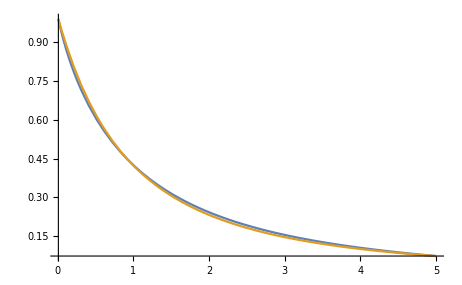

```mathematica
Plot[{ch[x]/.%78[[1]],1/(1+(Pi/8)^(2/3)x)^2},{x,.01,5}]
```

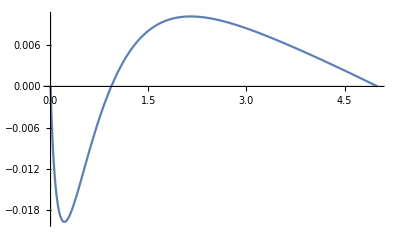

```mathematica
Plot[{(ch[x]/.%78[[1]])-1/(1+(Pi/8)^(2/3)x)^2},{x,.01,5}]
```